# Cosmomathica v1.0

Santiago Casas, 2020

This notebook demonstrates how to use the Cosmomathica package version 1.0

## Calling external programs

### Initialization

First, load the Cosmomathica package

```mathematica
SetDirectory[NotebookDirectory[]]
```

/local/home/scasas/CosmoProjects/cosmomathica

```mathematica
ManToGif[man_,name_String,step_Integer]:=Export[name<>".gif",Import[Export[FileNameJoin[{NotebookDirectory[],"temp.avi"}],man],"ImageList"][[1;;-1;;step]]];
```

```mathematica
<<(NotebookDirectory[]<>"cosmomathica.m")
```

```mathematica
<<NumericalCalculus`
```

### CAMB

CAMB takes a lot of parameters. In Cosmomathica, most of them are being treated as options with default values while some of them are regular parameters that have to be specified. The distinction is arbitrary. These are the default options (see the CAMB documentation for details):

```mathematica
?CAMB
```

CAMB[OmegaC, OmegaB, h] :
provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.

```mathematica
Options[CAMB]
```

{MGflag→0,pureMGflag→1,altMGflag→1,QSAflag→1,mugammapar→2,musigmapar→1,QRpar→1,DEmodel→1,GRtrans→0.001,B1→0.,lambda12→0.,B2→0.,lambda22→0.,ss→4.,E11→0.,E22→0.,mu0→-1.,sigma0→0.,MGQfix→0.,MGRfix→0.,Qnot→1.,Rnot→1.,sss→0.,Lindergamma→0.545,betastar→0.,astar→0.5,xistar→0.001,beta0→1.,xi0→0.0001,DilS→0.24,DilR→1.,FR0→0.0001,FRn→1.,w0ppf→-1.,wappf→0.,Tcmb→2.7255,OmegaNu→0,OmegaK0→0.,YHe→0.24,MasslessNeutrinos→3.046,MassiveNeutrinos→0,NuMassDegeneracies→{0},NuMassFractions→{1},ScalarInitialCondition→adiabatic,NonLinear→pk,HalofitVersion→4,WantCMB→True,WantTransfer→True,WantCls→False,WantScalars→False,WantVectors→False,WantTensors→False,ScalarSpectralIndex→{0.96},ScalarRunning→{0},TensorSpectralIndex→{0},RatioScalarTensorAmplitudes→{1},ScalarPowerAmplitude→{2.1×10^-9},PivotScalar→0.05,PivotTensor→0.05,DoReionization→True,UseOpticalDepth→False,OpticalDepth→0.,ReionizationRedshift→10.,ReionizationFraction→1.,ReionizationDeltaRedshift→0.5,AccuracyBoost→2,TransferHighPrecision→True,TransferInterpMatterPower→False,WantZstar→True,WantZdrag→True,OutputNormalization→1,MaxEll→1500,MaxEtaK→4000.,MaxEtaKTensor→800.,MaxEllTensor→400,TransferKmax→5,TransferKperLogInt→50,TransferRedshifts→{0.},AccuratePolarization→True,AccurateReionization→False,AccurateBB→False,DoLensing→False,OnlyTransfers→False,DerivedParameters→True,MassiveNuMethod→best,debugIntFloats→False}

```mathematica
OptionValue[CAMB,#]&/@{ScalarSpectralIndex,ScalarPowerAmplitude,TransferKmax, HalofitVersion, NonLinear}
```

{{0.96},{2.1×10^-9},5,4,pk}

```mathematica
OptionValue[CAMB,#]&/@{MGflag,pureMGflag,altMGflag,QSAflag,mugammapar,musigmapar,DEmodel,GRtrans,FR0,FRn,w0ppf,wappf}
```

{0,1,1,1,2,1,1,0.001,0.0001,1.,-1.,0.}

```mathematica
OptionValue[CAMB,#]&/@{Tcmb, OmegaNu,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions}
```

{2.7255,0,3.046,{0},{1}}

```mathematica
OptionValue[CAMB,#]&/@{AccuracyBoost,TransferHighPrecision,TransferInterpMatterPower}
```

{2,True,False}

```mathematica
?HalofitVersion
```

An option for CAMB. Integer number that chooses the Halofit version used in the non-linear matter power spectrum.
1: Original, 2: Bird, 3: Peacock, 4: Takahashi, 5: Mead, 6: Halo model, 7: Casarini,
8: Mead2015, 9: Winther-f(R)

```mathematica
redsub=Subdivide[0.,5.,99];
```

```mathematica
redshifts=Reverse[redsub(*Range[0,50,0.1]*)(*Join~{20,100}*)];
```

```mathematica
redzrang=Range[Length[redshifts]];
```

```mathematica
ClearAll[cambdata]
```

```mathematica
computeOmegaCNuParams[OmegaM_, OmegaB_, hubble_, MnuTotal_]:=Block[{Neff = 3.046, omgref,OmegaRDS, masslessnus, 
numassfac=94.07(*eV*), massivenus, omeganuh2,
OmegaNu, OmegaC},
Which[
MnuTotal==0.06,
massivenus=1; 
,
MnuTotal==0.15,
massivenus=3; 
,
MnuTotal==0.,
massivenus=0; 
];
omgref = (2.469/hubble^2)*10^(-5);
OmegaRDS = omgref*(1. + 0.2271*Neff);
masslessnus=Neff-massivenus;
omeganuh2=Sum[(((Neff/3)^(3/4))*(MnuTotal/massivenus))/numassfac, {i,1,massivenus}];
OmegaNu=omeganuh2/(hubble^2);
OmegaC=OmegaM-OmegaB-OmegaNu;
Return[{OmegaC, OmegaNu, massivenus, masslessnus}]
];

ClearAll[kvals,psl, psnl, growthCAMB, fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin, s8growth, s8fgrowthrate, Hofz, redshiftsz, scalefactor]
fillCosmoData[totalmodlist_, cambdata_]:=Block[{test},
Do[
redshiftsz[ii_]:=(CAMB["redshifts"]/.cambdata[ii]);
scalefactor[ii_][zind_]:=(1/redshiftsz[0][[zind]]);
kvals[ii_]:=((CAMB["PSlinear"]/.cambdata[ii])[[1,All,1]]);
psl[ii_][zind_,kind_]:=((CAMB["PSlinear"]/.cambdata[ii])[[zind,kind,2]]);
psnl[ii_][zind_,kind_]:=((CAMB["PSnonlinear"]/.cambdata[ii])[[zind,kind,2]]);
growthCAMB[ii_][zind_,kind_]:=(((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,7]])/((CAMB["Transfer"]/.cambdata[ii])[[-1, kind,7]]));
fgrowthrateCAMB[ii_][zind_,kind_]:=((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,14]])/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]]);
s8growth[ii_][zind_]:=((CAMB["D+(z)"]/.cambdata[ii])[[zind]]);
s8fgrowthrate[ii_][zind_]:=((CAMB["f(z)"]/.cambdata[ii])[[zind]]);
growthRatioPksLin[ii_][zind_,kind_]:=Sqrt[psl[ii][zind,kind]/psl[ii][-1,kind]];
growthRatioPksNonLin[ii_][zind_,kind_]:=Sqrt[psnl[ii][zind,kind]/psnl[ii][-1,kind]];
Hofz[ii_][zind_]:=((CAMB["H(z)"]/.cambdata[ii])[[zind]]);
,
{ii,totalmodlist}]
]
```

```mathematica
(*Standard LCDM, massless neutrinos*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]

cambdata[0]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}, TransferKmax->50,TransferKperLogInt->50 ];

(CAMB["sigma8(z)"]/.cambdata[0])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

0.824897

```mathematica
cambdata[0][[All,1]]
```

{CAMB[age],CAMB[zstar],CAMB[rstar],CAMB[100thetastar],CAMB[zdrag],CAMB[rdrag],CAMB[kD],CAMB[100thetaD],CAMB[zEQ],CAMB[100thetaEQ],CAMB[H(z)],CAMB[sigma8(z)],CAMB[f(z)],CAMB[D+(z)],CAMB[CLscalar],CAMB[redshifts],CAMB[PSlinear],CAMB[PSnonlinear],CAMB[Transfer]}

```mathematica
(*Standard LCDM, massive neutrinos, MntTotal=0.06eV*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[1]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->4,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}, TransferKmax->50,TransferKperLogInt->50 ];

(CAMB["sigma8(z)"]/.cambdata[1])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.810567

```mathematica
(*(* w0waCDM , non-Lambda, massless neutrinos, MNuTotal=0eV, HalofitVersion=Mead (=5)*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-0.9; weqa=0.05;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.0; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[2]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}, w0ppf->weq0, wappf->weqa,DEmodel->1];

(CAMB["sigma8(z)"]/.cambdata[2])[[-1]]*)
```

```mathematica
(*(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[34]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-4), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[34])[[-1]]*)
```

```mathematica
(*(*f(R) theory, massless neutrinos, fR0=10^-5*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[35]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-5), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[35])[[-1]]*)
```

```mathematica
(*f(R) theory, massive neutrinos, fR0=10^-5*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)
fR0=5*10^(-5);

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[51]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->fR0, FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, 
 OmegaNu->OmegaNuref,NuMassFractions->{1}, TransferKmax->50,TransferKperLogInt->50, GRtrans->0.001(*1.0*)(*(*0.001*)0.218*)];

(CAMB["sigma8(z)"]/.cambdata[51])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.905425

```mathematica
(*f(R) theory, massive neutrinos, fR0=10^-8*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)
fR0=5*10^(-8);

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[81]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->fR0, FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, 
 OmegaNu->OmegaNuref,NuMassFractions->{1}, TransferKmax->50,TransferKperLogInt->50, GRtrans->0.001(*1.0*)(*(*0.001*)0.218*)];

(CAMB["sigma8(z)"]/.cambdata[81])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.268563

OmegaB= 0.05

OmegaNu= 0.00143717

Massless Nus = 2.046

0.811462

```mathematica
(*f(R) theory, massless neutrinos, fR0=10^-8*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)
fR0=5*10^(-8);

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[80]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->fR0, FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, 
 OmegaNu->OmegaNuref,NuMassFractions->{1}, TransferKmax->50,TransferKperLogInt->50, GRtrans->0.001(*1.0*)(*0.001(*0.218*)*)];

(CAMB["sigma8(z)"]/.cambdata[80])[[-1]]
```

OmegaM= 0.32

OmegaC= 0.27

OmegaB= 0.05

OmegaNu= 0.

Massless Nus = 3.046

0.825807

```mathematica
(*(*f(R) theory, massless neutrinos, fR0=10^-4*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[36]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True,
 HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-6), FRn->1, DEmodel->0, MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1}];

(CAMB["sigma8(z)"]/.cambdata[36])[[-1]]*)
```

```mathematica
(*(* ModifiedGravity, muGamma Parametrization, LCDM background,  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2, massless neutrinos, HalofitVersion=4 Takahashi*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.0; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[4]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1},  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2 ];

(CAMB["sigma8(z)"]/.cambdata[4])[[-1]]*)
```

```mathematica
(*(* ModifiedGravity, muGamma Parametrization, LCDM background,  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2, massless neutrinos, HalofitVersion=4 Takahashi*)
nsref=0.96; 
as109ref=2.12605;
Asref=as109ref*10^-9;
hubbleref=0.67; 
weq0=-1.0; weqa=0.;
OmegaMref=0.320; 
OmegaBref=0.050;
Mnutotalref=0.06; (*eV*)

{OmegaCref,OmegaNuref,massivenus,masslessnus} = computeOmegaCNuParams[OmegaMref, OmegaBref, hubbleref, Mnutotalref];

Print["OmegaM= ", OmegaMref]
Print["OmegaC= ", OmegaCref]
Print["OmegaB= ", OmegaBref]
Print["OmegaNu= ", OmegaNuref]
Print["Massless Nus = ", masslessnus];

cambdata[4]=CAMB[OmegaCref,OmegaBref,hubbleref,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->5,
MasslessNeutrinos->masslessnus, MassiveNeutrinos->massivenus, OmegaNu->OmegaNuref,NuMassFractions->{1},  HalofitVersion->4, MGflag->1, pureMGflag->1,
 DEmodel->0, GRtrans->0.001, E11->0.1007, E22->0.8293, mugammapar ->2 ];

(CAMB["sigma8(z)"]/.cambdata[4])[[-1]]*)
```

```mathematica
(*Do[
Print["ii:", ii];
cambdata[ii]=CAMB[0.25,0.05,0.67,TransferRedshifts->redshifts, WantCls->True,WantScalars->True, HalofitVersion->9, MGflag->3, QSAflag->4, FR0->10^(-ii), FRn->1, DEmodel->0];
,{ii,{4,5,6}}]*)
```

```mathematica
redshifts=CAMB["redshifts"]/.cambdata[0]
```

{5.,4.94949,4.89899,4.84848,4.79798,4.74747,4.69697,4.64646,4.59596,4.54545,4.49495,4.44444,4.39394,4.34343,4.29293,4.24242,4.19192,4.14141,4.09091,4.0404,3.9899,3.93939,3.88889,3.83838,3.78788,3.73737,3.68687,3.63636,3.58586,3.53535,3.48485,3.43434,3.38384,3.33333,3.28283,3.23232,3.18182,3.13131,3.08081,3.0303,2.9798,2.92929,2.87879,2.82828,2.77778,2.72727,2.67677,2.62626,2.57576,2.52525,2.47475,2.42424,2.37374,2.32323,2.27273,2.22222,2.17172,2.12121,2.07071,2.0202,1.9697,1.91919,1.86869,1.81818,1.76768,1.71717,1.66667,1.61616,1.56566,1.51515,1.46465,1.41414,1.36364,1.31313,1.26263,1.21212,1.16162,1.11111,1.06061,1.0101,0.959596,0.909091,0.858586,0.808081,0.757576,0.707071,0.656566,0.606061,0.555556,0.505051,0.454545,0.40404,0.353535,0.30303,0.252525,0.20202,0.151515,0.10101,0.0505051,0.}

```mathematica
redshifts//Dimensions
```

{100}

```mathematica
transfer=CAMB["Transfer"]/.cambdata[0];
```

```mathematica
transfer//Dimensions
```

{100,478,14}

```mathematica
(* redshifts length, k-values length and 14 transfer quantities*)
```

```mathematica
kvalues = transfer[[1,All,1]];
```

```mathematica
kvalues//Dimensions
```

{478}

```mathematica
MinMax@kvalues
```

{5.2782×10^-6,50.8091}

```mathematica
(*Total[Chop[kvalues-kvaluesFromPk, 10^-10]]*)
```

```mathematica
(*Interrupt[]*)
```

## Compute Interpolated Quantities and Arrays

```mathematica
totalmodlist={0,1, 51, 80, 81}
```

{0,1,51,80,81}

```mathematica
(*modelsname={"LCDM","LCDM_Mν","w0waCDM","MG_μ-η", "f(R)-4", "f(R)-5","f(R)-5_Mν",  "f(R)-6"}*)
```

```mathematica
modelsname={"LCDM","LCDM_Mν",  "f(R)_HS5_Mν", "f(R)_HS8",  "f(R)_HS8_Mν"}
```

{LCDM,LCDM_Mν,f(R)_HS5_Mν,f(R)_HS8,f(R)_HS8_Mν}

```mathematica
fillCosmoData[totalmodlist, cambdata]
```

```mathematica
redshiftsz[0]
```

{50.,49.4949,48.9899,48.4848,47.9798,47.4747,46.9697,46.4646,45.9596,45.4545,44.9495,44.4444,43.9394,43.4343,42.9293,42.4242,41.9192,41.4141,40.9091,40.404,39.899,39.3939,38.8889,38.3838,37.8788,37.3737,36.8687,36.3636,35.8586,35.3535,34.8485,34.3434,33.8384,33.3333,32.8283,32.3232,31.8182,31.3131,30.8081,30.303,29.798,29.2929,28.7879,28.2828,27.7778,27.2727,26.7677,26.2626,25.7576,25.2525,24.7475,24.2424,23.7374,23.2323,22.7273,22.2222,21.7172,21.2121,20.7071,20.202,19.697,19.1919,18.6869,18.1818,17.6768,17.1717,16.6667,16.1616,15.6566,15.1515,14.6465,14.1414,13.6364,13.1313,12.6263,12.1212,11.6162,11.1111,10.6061,10.101,9.59596,9.09091,8.58586,8.08081,7.57576,7.07071,6.56566,6.06061,5.55556,5.05051,4.54545,4.0404,3.53535,3.0303,2.52525,2.0202,1.51515,1.0101,0.505051,0.}

```mathematica
{kvals,psl, psnl, growthCAMB, fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin, s8growth, s8fgrowthrate, Hofz, redshiftsz}
```

{kvals,psl,psnl,growthCAMB,fgrowthrateCAMB,growthRatioPksLin,growthRatioPksNonLin,s8growth,s8fgrowthrate,Hofz,redshiftsz}

```mathematica
(*reshap=ArrayReshape[growthTab[0][[All,2]], {Length@revZrang[0], Length@krang[0]}];
reshap//Dimensions*)
```

```mathematica
ClearAll[revZrang];  ClearAll["*Interp"]; ClearAll["*Tab"]; ClearAll[krang];
```

ClearAll::wrsym: Symbol Tab is Protected.

```mathematica
krang[mod_]:=krang[mod]=Range[Length[kvals[mod]]];
revZrang[mod_]:=revZrang[mod]=Reverse[Range[Length[redshiftsz[mod]]]];
growthCAMBTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthCAMB[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthCAMBInterp[mod_]:=growthCAMBInterp[mod]=Interpolation[growthCAMBTab[mod], InterpolationOrder->3, Method->"Spline"];
fgrowthrateCAMBTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},fgrowthrateCAMB[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
fgrowthrateCAMBInterp[mod_]:=fgrowthrateCAMBInterp[mod]=Interpolation[fgrowthrateCAMBTab[mod], InterpolationOrder->3, Method->"Spline"];
pkLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1];
pkNonLinTab[mod_]:=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},psnl[mod][zzi,kki]},{zzi,Range[Length[redshiftsz[mod]]]},{kki, Range[Length[kvals[mod]]]}],1];
pkLinInterp[mod_]:=pkLinInterp[mod]=Interpolation[pkLinTab[mod], InterpolationOrder->1, Method->"Spline"];
pkNonLinInterp[mod_]:=pkNonLinInterp[mod]=Interpolation[pkNonLinTab[mod], InterpolationOrder->1, Method->"Spline"];

s8growthInterp[mod_]:=s8growthInterp[mod]=Interpolation[Table[{redshiftsz[mod][[zzi]],s8growth[mod][zzi]}, {zzi,1,Length[redshiftsz[mod]]}], InterpolationOrder->3, Method->"Spline"];
s8fgrowthrateInterp[mod_]:=s8fgrowthrateInterp[mod]=Interpolation[Table[{redshiftsz[mod][[zzi]],s8fgrowthrate[mod][zzi]}, {zzi,1,Length[redshiftsz[mod]]}], InterpolationOrder->3, Method->"Spline"];


growthRatioPksLinTab[mod_]:=growthRatioPksLinTab[mod]=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthRatioPksLin[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthRatioPksLinTabInterp[mod_]:=growthRatioPksLinTabInterp[mod]=Interpolation[growthRatioPksLinTab[mod], InterpolationOrder->3, Method->"Spline"];

growthRatioPksNonLinTab[mod_]:=growthRatioPksNonLinTab[mod]=Flatten[Table[{{redshiftsz[mod][[zzi]], kvals[mod][[kki]]},growthRatioPksNonLin[mod][zzi,kki]},{zzi,revZrang[mod]},{kki,krang[mod] }],1];
growthRatioPksNonLinTabInterp[mod_]:=growthRatioPksNonLinTabInterp[mod]=Interpolation[growthRatioPksNonLinTab[mod], InterpolationOrder->3, Method->"Spline"];

fgRatioPksLinInterp[mod_][z_, ka_]:=Block[{zz},-(1+z)*ND[Log[growthRatioPksLinTabInterp[mod][zz,ka]],zz,z]];
fgRatioPksNonLinInterp[mod_][z_, ka_]:=Block[{zz},-(1+z)*ND[Log[growthRatioPksNonLinTabInterp[mod][zz,ka]],zz,z]];
```

```mathematica
Interrupt[]
```

$Aborted

## Plot Functions

```mathematica
totalmodlist
```

{0,1,51,80,81}

```mathematica
lenmod=Length@totalmodlist;
colorarra=ColorData["DarkRainbow"][#]&/@Subdivide[1,lenmod-1];
modelsnamerule=Thread[Rule[totalmodlist,modelsname]];
overallStyles=Thread[{ConstantArray[Thick,Length@colorarra],Thread[{colorarra,Table[AbsoluteDashing[{r,lenmod-r}],{r,Range[lenmod]}]}]}]
```

{{Thickness[Large],{RGBColor[0.237736, 0.340215, 0.575113],AbsoluteDashing[{1,4}]}},{Thickness[Large],{RGBColor[0.277947, 0.45009699999999997, 0.32815550000000004],AbsoluteDashing[{2,3}]}},{Thickness[Large],{RGBColor[0.624866, 0.673302, 0.264296],AbsoluteDashing[{3,2}]}},{Thickness[Large],{RGBColor[0.8453409999999999, 0.6248695, 0.3151775],AbsoluteDashing[{4,1}]}},{Thickness[Large],{RGBColor[0.72987, 0.239399, 0.230961],AbsoluteDashing[{5,0}]}}}

```mathematica
ClearAll[raplonl];
```

```mathematica
raplonl[modlist_,zz_,lin_?BooleanQ, kmax_, plrang_:Full]:=Block[{pk, basemodel=modlist[[1]]},
If[lin,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@(((pk[#][zz,kkk]/pk[basemodel][zz,kkk])&/@modlist)) ,
{kkk,0.0001,kmax}, Frame->True, FrameLabel->{"", Style["P_model(k)/P_LCDM(k)", Bold, 10]} , 
ImageSize->{300,150}, FrameTicksStyle->Directive[Black,10],
PlotStyle->overallStyles, PlotRange->plrang]];
```

```mathematica
(*raplonl[{0,1,2,3,4},0.,True]*)
```

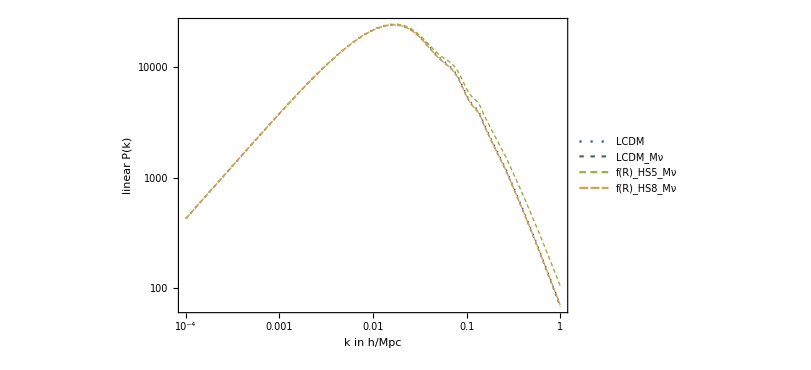

```mathematica
ClearAll[pk];
linBool=True;
plotmodlist={0,1,51, 81};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,1.0},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["linear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, 1.0], Scaled[{0.5,0.3}]]]
```

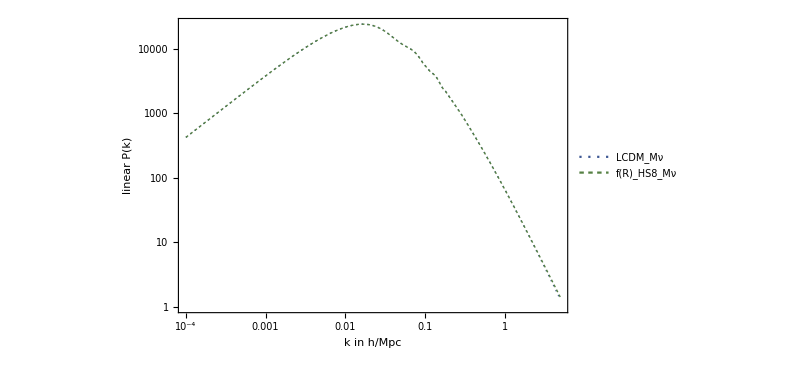

```mathematica
ClearAll[pk];
linBool=True;
plotmodlist={1,81};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["linear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, 5, {0.99,1.1}], Scaled[{0.5,0.3}]]]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,80→f(R)_HS8,81→f(R)_HS8_Mν}

```mathematica
(*ClearAll[pk];
linBool=True;
plotmodlist={0,1};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.85,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["linear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, {0.9,1.1}], Scaled[{0.5,0.3}]]]*)
```

```mathematica
(*ClearAll[pk];
linBool=True;
plotmodlist={0,2};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,4},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.1,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["nonlinear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, {0.9,1.1}], Scaled[{0.5,0.3}]]]*)
```

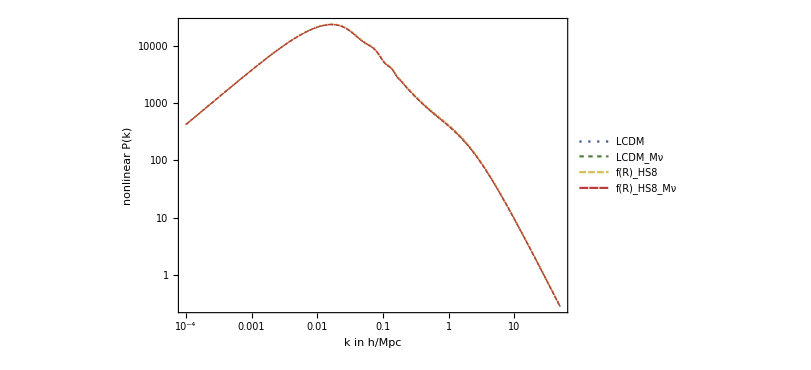

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,80,81};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,50.}, 
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["nonlinear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, 50., {0.95,1.02}], Scaled[{0.5,0.3}]]]
```

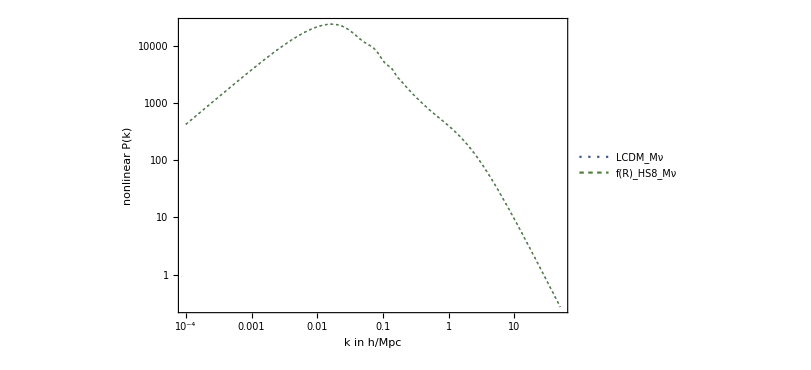

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={1,81};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLogPlot[Evaluate@((pk[#][zplot,kkk]&/@plotmodlist)), {kkk,0.0001,50.},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["nonlinear P(k)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],Epilog->Inset[raplonl[plotmodlist,zplot,linBool, 50., {0.99,1.03}], Scaled[{0.5,0.3}]]]
```

```mathematica
overallPlotRange={0.2,1.1};
```

```mathematica
ztoa[zz_]:=1/(1+zz)
```

```mathematica
atoz[aa_]:=(1/aa)-1
```

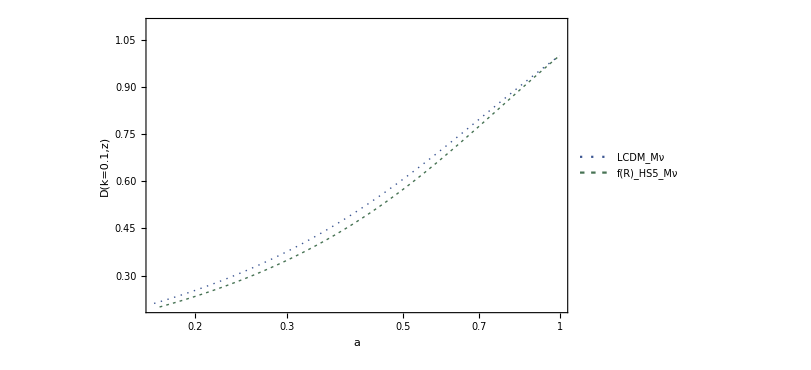

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={1,51};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][atoz[aa], 0.1]&/@plotmodlist)), {aa,ztoa[0.0001],ztoa[5.0]}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.25}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["a", Bold,16], Style["D(k=0.1,z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

```mathematica
(*ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zz, 0.0005]&/@plotmodlist)), {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["D(k=0.001,z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]*)
```

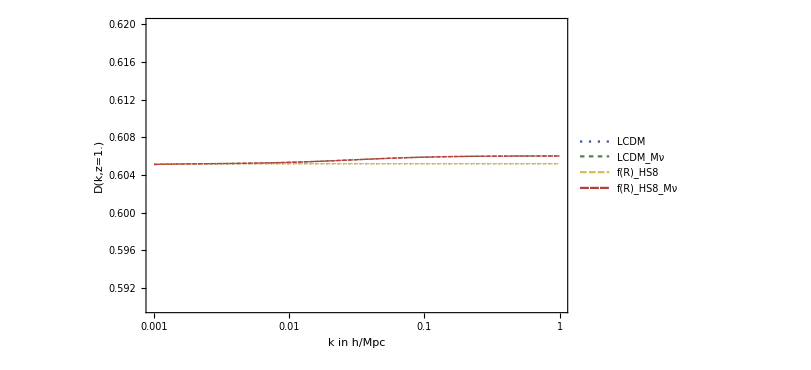

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,80,81};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.001,1.0},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->{0.59,0.62}]
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,80→f(R)_HS8,81→f(R)_HS8_Mν}

```mathematica
(*ClearAll[pk];
linBool=False;
plotmodlist={0,1,34, 35,351, 36};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->{0.55,0.65}]*)
```

```mathematica
(*ClearAll[pk];
linBool=False;
plotmodlist={0,1};
zplot=1.0;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((growthCAMBInterp[#][zplot, kkk]&/@plotmodlist)), {kkk,0.0001,5},
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k,z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16](*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*), PlotRange->Full]*)
```

```mathematica
modelsnamerule
```

{0→LCDM,1→LCDM_Mν,80→f(R)_HS8,81→f(R)_HS8_Mν}

```mathematica
(*manDkzFR=Manipulate[LogLogPlot[{growthCAMBInterp[0][zvalue,kkk],growthCAMBInterp[2][zvalue,kkk],growthCAMBInterp[4][zvalue,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "MGmugamma"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "D(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[zvalue], Bold, 14],Scaled[{0.2,0.2}]], 
PlotRange->{0.4,1.05}      ],{zvalue, 0.001,10, 0.01}]*)
```

```mathematica
(*modelsnamerule*)
```

```mathematica
(*manfgkzFR=Manipulate[LogLogPlot[{fgrowthrateCAMBInterp[0][zvalue,kkk],fgrowthrateCAMBInterp[2][zvalue,kkk],fgrowthrateCAMBInterp[4][zvalue,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "MGmugamma"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[zvalue], Bold, 14],Scaled[{0.2,0.2}]], 
PlotRange->{0.4,1.05}      ],{zvalue, 0.001,10, 0.01}]*)
```

```mathematica
overallPlotRange={0.2,1.1};
```

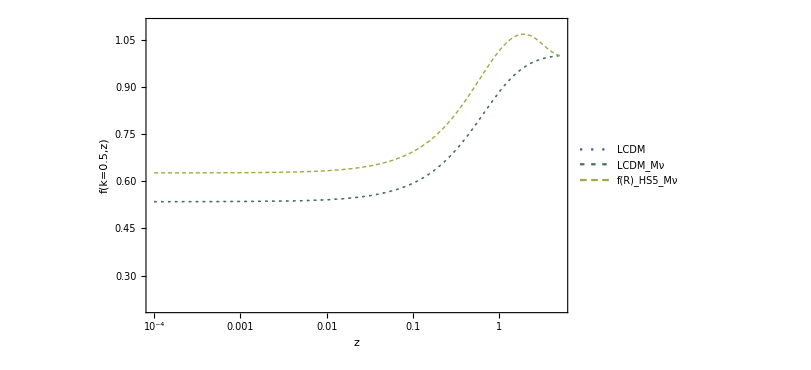

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={0,1,51};
zplot=0.5;
kplot=0.5;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

```mathematica
(*ClearAll[pk];
linBool=False;
plotmodlist={0,1,2,3,4};
zplot=0.;
kplot=0.0001;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]*)
```

```mathematica
(*ClearAll[pk];
linBool=False;
plotmodlist={0,1};
zplot=0.;
kplot=0.2;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->Full(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]*)
```

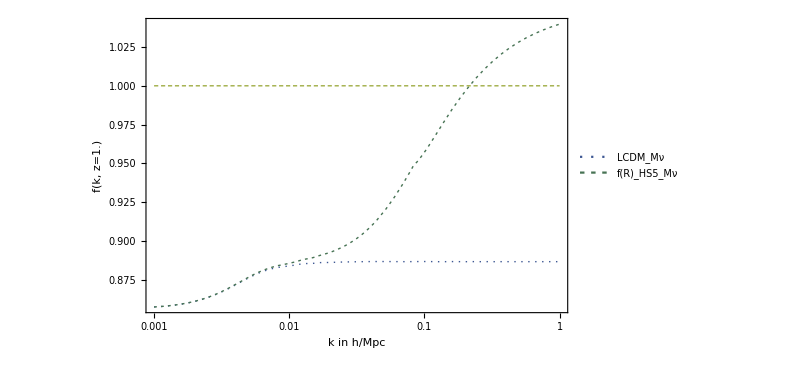

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={1,51}(*{0,1, 80, 81*);
zplot=1.0;
kplot=0.0001;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@(((fgrowthrateCAMBInterp[#][zplot, kk]&/@plotmodlist))~Join~{1}), {kk,0.001,1.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["f(k, z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->Full(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

```mathematica
a=(1/(zplot+1))
```

0.25

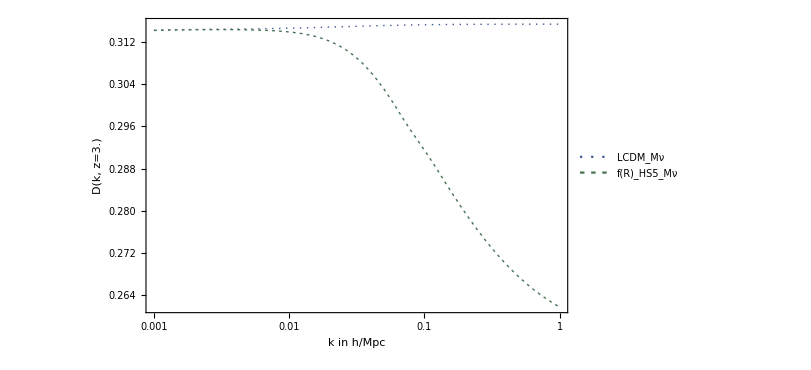

```mathematica
ClearAll[pk];
linBool=False;
plotmodlist={1,51}(*{0,1, 80, 81*);
zplot=3.0;
kplot=0.0001;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@(((growthCAMBInterp[#][zplot, kk]&/@plotmodlist))), {kk,0.001,1.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style["D(k, z="<>ToString[zplot]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->Full(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

```mathematica
ND[growthCAMBInterp[51][zz, 0.01],zz,0.1]
```

-0.514785

```mathematica
fderiv[z_,kk_,mod_]:=-(1+z)(ND[growthCAMBInterp[mod][zz, kk],zz,z])/growthCAMBInterp[51][z, 0.01]
```

```mathematica
fderiv[0.1, 0.2, 51]
```

0.684262

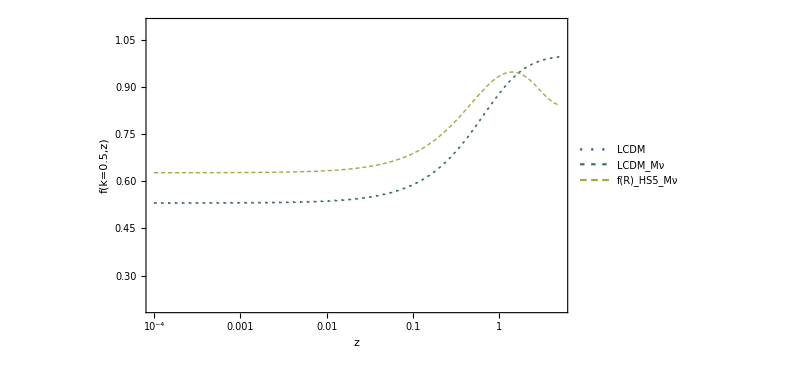

```mathematica
linBool=False;
plotmodlist={0,1, 51};
zplot=0.5;
kplot=0.5;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@(((*fgrowthrateCAMBInterp[#][zz, kplot]*)fderiv[zz, kplot, #]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

```mathematica
redshiftsz[51]
```

{5.,4.94949,4.89899,4.84848,4.79798,4.74747,4.69697,4.64646,4.59596,4.54545,4.49495,4.44444,4.39394,4.34343,4.29293,4.24242,4.19192,4.14141,4.09091,4.0404,3.9899,3.93939,3.88889,3.83838,3.78788,3.73737,3.68687,3.63636,3.58586,3.53535,3.48485,3.43434,3.38384,3.33333,3.28283,3.23232,3.18182,3.13131,3.08081,3.0303,2.9798,2.92929,2.87879,2.82828,2.77778,2.72727,2.67677,2.62626,2.57576,2.52525,2.47475,2.42424,2.37374,2.32323,2.27273,2.22222,2.17172,2.12121,2.07071,2.0202,1.9697,1.91919,1.86869,1.81818,1.76768,1.71717,1.66667,1.61616,1.56566,1.51515,1.46465,1.41414,1.36364,1.31313,1.26263,1.21212,1.16162,1.11111,1.06061,1.0101,0.959596,0.909091,0.858586,0.808081,0.757576,0.707071,0.656566,0.606061,0.555556,0.505051,0.454545,0.40404,0.353535,0.30303,0.252525,0.20202,0.151515,0.10101,0.0505051,0.}

```mathematica
linBool=False;
plotmodlist={0,1, 51};
zplot=0.5;
kplot=0.5;
If[linBool,pk=pkLinInterp,pk=pkNonLinInterp];
LogLinearPlot[Evaluate@((fgrowthrateCAMBInterp[#][zz, kplot]&/@plotmodlist)), {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[plotmodlist/.modelsnamerule], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

-Graphics-

```mathematica
kvals[51][[250]]
```

0.531416

```mathematica
redshiftsz[51][[1]]
```

5.

```mathematica
lista1=((CAMB["Transfer"]/.cambdata[51])[[All, 250,14]])(*/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]])*)
```

{7.90292,7.90635,7.90998,7.91381,7.91786,7.92214,7.92665,7.93141,7.93643,7.94171,7.94726,7.95311,7.95924,7.96569,7.97244,7.97952,7.98693,7.99468,8.00276,8.0112,8.01999,8.02913,8.03862,8.04847,8.05867,8.06923,8.08012,8.09135,8.1029,8.11476,8.12692,8.13936,8.15206,8.165,8.17815,8.19148,8.20497,8.21858,8.23227,8.24602,8.25977,8.27349,8.28713,8.30064,8.31398,8.32709,8.33991,8.3524,8.36448,8.37611,8.38721,8.39772,8.40758,8.4167,8.42502,8.43245,8.43893,8.44435,8.44864,8.4517,8.45343,8.45372,8.45247,8.44956,8.44487,8.43825,8.42957,8.41867,8.40539,8.38955,8.37095,8.34939,8.32464,8.29645,8.26456,8.22867,8.18848,8.14365,8.09379,8.03852,7.97741,7.90997,7.83572,7.75411,7.66457,7.5665,7.45926,7.34219,7.2146,7.0758,6.92509,6.76182,6.58534,6.39509,6.19059,5.97151,5.73766,5.48907,5.22601,4.94905}

```mathematica
lista2=((CAMB["Transfer"]/.cambdata[51])[[1, 250,14]])(*/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]])*)
```

7.90292

```mathematica
lista1//Dimensions
```

{100}

```mathematica
redshiftsz[51];
```

```mathematica
lista1/7.90292
```

{1.,1.00043,1.00089,1.00138,1.00189,1.00243,1.003,1.00361,1.00424,1.00491,1.00561,1.00635,1.00713,1.00794,1.0088,1.00969,1.01063,1.01161,1.01263,1.0137,1.01481,1.01597,1.01717,1.01842,1.01971,1.02104,1.02242,1.02384,1.0253,1.02681,1.02834,1.02992,1.03153,1.03316,1.03483,1.03651,1.03822,1.03994,1.04167,1.04341,1.04515,1.04689,1.04862,1.05033,1.05201,1.05367,1.0553,1.05687,1.0584,1.05988,1.06128,1.06261,1.06386,1.06501,1.06606,1.067,1.06782,1.06851,1.06905,1.06944,1.06966,1.0697,1.06954,1.06917,1.06858,1.06774,1.06664,1.06526,1.06358,1.06158,1.05922,1.05649,1.05336,1.0498,1.04576,1.04122,1.03613,1.03046,1.02415,1.01716,1.00943,1.00089,0.991496,0.98117,0.969841,0.957431,0.943862,0.929048,0.912903,0.895339,0.87627,0.85561,0.833279,0.809205,0.78333,0.755608,0.726017,0.694562,0.661276,0.626231}

```mathematica
(fgrowthrateCAMBInterp[51][#, kplot]&/@redshiftsz[51] - lista1/7.90292)/(lista1/7.90292)
```

{2.91934×10^-8,-0.0000505574,-0.000103219,-0.000157878,-0.000214327,-0.000272993,-0.000333492,-0.000395874,-0.000460229,-0.000526443,-0.000594456,-0.000664178,-0.000735515,-0.000808359,-0.000882426,-0.00095773,-0.00103413,-0.00111135,-0.00118891,-0.00126707,-0.00134517,-0.00142303,-0.00150043,-0.00157703,-0.00165251,-0.00172634,-0.00179823,-0.00186798,-0.00193534,-0.0019997,-0.00206054,-0.00211786,-0.0021713,-0.00222044,-0.00226483,-0.00230458,-0.00233919,-0.00236853,-0.00239246,-0.00241082,-0.00242362,-0.0024305,-0.00243173,-0.00242711,-0.00241693,-0.00240113,-0.00237963,-0.00235294,-0.00232111,-0.00228417,-0.00224251,-0.00219638,-0.00214602,-0.0020917,-0.00203354,-0.00197217,-0.00190761,-0.00184033,-0.00177058,-0.0016984,-0.0016245,-0.00154909,-0.00147217,-0.00139429,-0.00131567,-0.0012364,-0.00115685,-0.00107736,-0.000998108,-0.000919061,-0.000840746,-0.000763223,-0.000686448,-0.000610928,-0.000536696,-0.000463826,-0.000392522,-0.000322793,-0.000254864,-0.000188672,-0.000124651,-0.0000623115,-2.19687×10^-6,0.0000557174,0.000111491,0.000165113,0.000216374,0.000265444,0.000312006,0.000356332,0.000398222,0.000437828,0.00047507,0.000509755,0.000541938,0.000571942,0.000599317,0.00062418,0.00064679,0.000666425}

```mathematica
Max[lista1]
```

8.45372

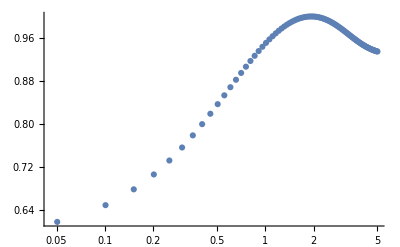

```mathematica
listaplot=ListLogLinearPlot[Transpose[{redshiftsz[51], lista1/Max[lista1]}], PlotRange->Full]
```

```mathematica
kplot=kvals[51][[250]]
```

0.531416

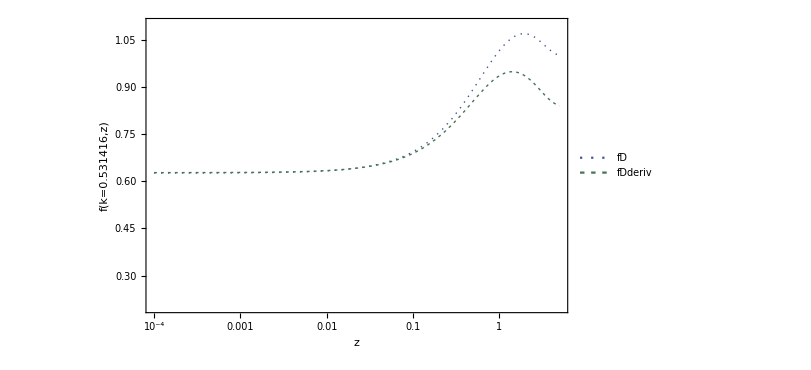

```mathematica
funcplot=LogLinearPlot[Evaluate@{(fgrowthrateCAMBInterp[51][zz, kplot]),fderiv[zz, kplot, 51]} , {zz,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"fD","fDderiv"}], Scaled[{0.15,0.8}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style["f(k="<>ToString[kplot]<>",z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->overallPlotRange(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

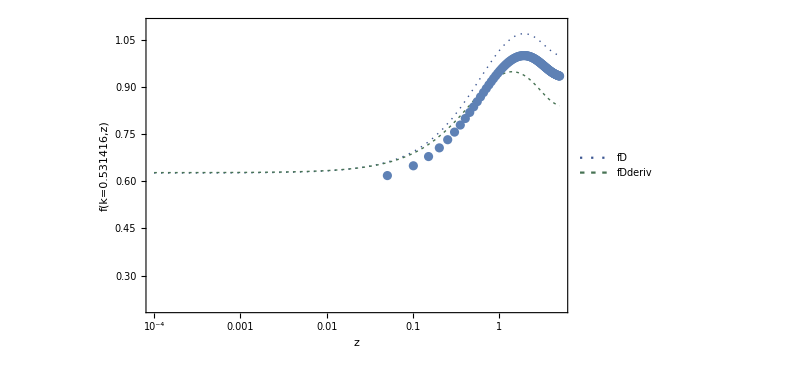

```mathematica
Show[funcplot, listaplot]
```

```mathematica
(*fgrowthrateCAMB[ii_][zind_,kind_]:=((CAMB["Transfer"]/.cambdata[ii])[[zind, kind,14]])/((CAMB["Transfer"]/.cambdata[ii])[[1, kind,14]])*)
```

## Plot different options for Growth

```mathematica
(*ManToGif[manDkzFR,FileNameJoin[{NotebookDirectory[],"Dkz-fR"}],1]*)
```

```mathematica
(*manFzkFR=Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogPlot[{growthrateCAMBInterp[4][zzz,kpoint],fgInterp[4][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogPlot[{growthrateCAMBInterp[6][zzz,kpoint]/fgInterp[6][zzz,kpoint]}, {zzz,0.,10.0}, PlotLegends->{"f4-camb", "f4-deriv"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->All  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*ManToGif[manFzkFR,FileNameJoin[{NotebookDirectory[],"fG_zk-fR"}],1]*)
```

```mathematica
(*Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]*)
```

```mathematica
(*Manipulate[LogPlot[{fgInterp[0][zzz,kpoint],fgInterp[4][zzz,kpoint],fgInterp[6][zzz,kpoint], s8growthrateInterp[4][zzz]}, {zzz,0.,10.0}, PlotLegends->{"LCDM", "logfR0=-4", "logfR0=-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["z", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["k="<>ToString[N@kpoint]<>"  Mpc^-1", Bold, 14],Scaled[{0.8,0.2}]]    , PlotRange->{0.8,1.2}  ], {kpoint, 10^-4,2,0.001}]*)
```

```mathematica
(*Manipulate[LogLinearPlot[{fgInterp[0][zpoint,kkk],fgInterp[4][zpoint,kkk],fgInterp[6][zpoint,kkk], s8growthrateInterp[4][zpoint]}, {kkk,0.0001,4.0}, PlotLegends->{"LCDM", "fR0=10^-4", "fR0=10^-6", "k=s8_logfR0=-4"}, PlotStyle->AbsoluteThickness[2],AxesLabel->{Style["k", Bold,16],Style[ "f(z,k)", Bold, 16]}, Epilog->Inset[Style["z="<>ToString[N@zpoint], Bold, 14],Scaled[{0.8,0.2}]]    (*PlotRange->{0.8,1.2}*)  ], {zpoint, 0.,9.9}]*)
```

```mathematica
Names["*Interp"]
```

{fgRatioPksLinInterp,fgRatioPksNonLinInterp,fgrowthrateCAMBInterp,growthCAMBInterp,growthRatioPksLinTabInterp,growthRatioPksNonLinTabInterp,pkLinInterp,pkNonLinInterp,s8fgrowthrateInterp,s8growthInterp}

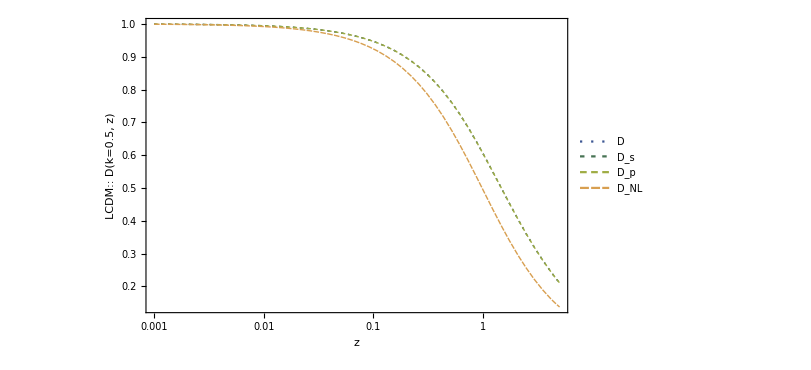

```mathematica
modelnum=0;
modelname=modelnum/.modelsnamerule;
kvall=0.5;
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall], growthRatioPksNonLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p", "D_NL"}], Scaled[{0.15,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

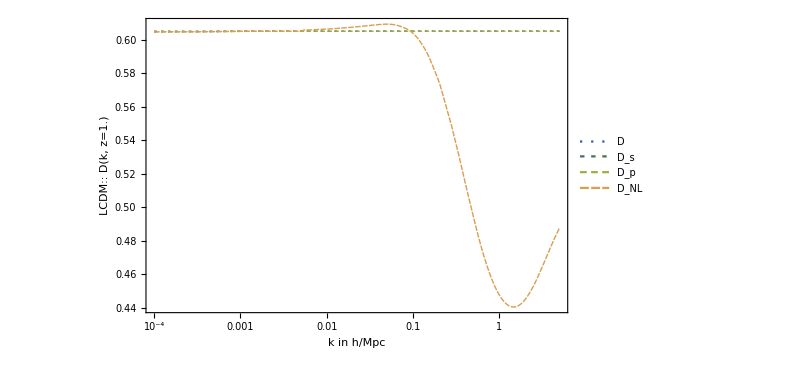

```mathematica
modelnum=0;
modelname=modelnum/.modelsnamerule;
kvall=0.5;
zvall=1.0;
LogLinearPlot[{growthCAMBInterp[modelnum][zvall, kk],s8growthInterp[modelnum][zvall],growthRatioPksLinTabInterp[modelnum][zvall,kk], growthRatioPksNonLinTabInterp[modelnum][zvall,kk]}, {kk,0.0001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p", "D_NL"}], Scaled[{0.15,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"D(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

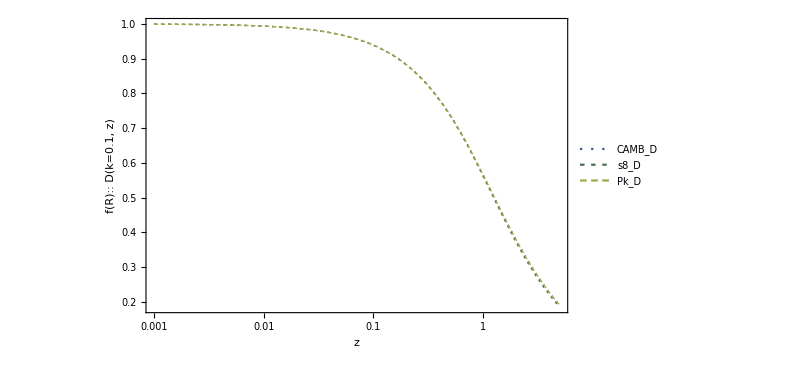

```mathematica
modelnum=3;
modelname=modelnum/.modelsnamerule;
kvall=0.1;
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"CAMB_D","s8_D","Pk_D"}], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

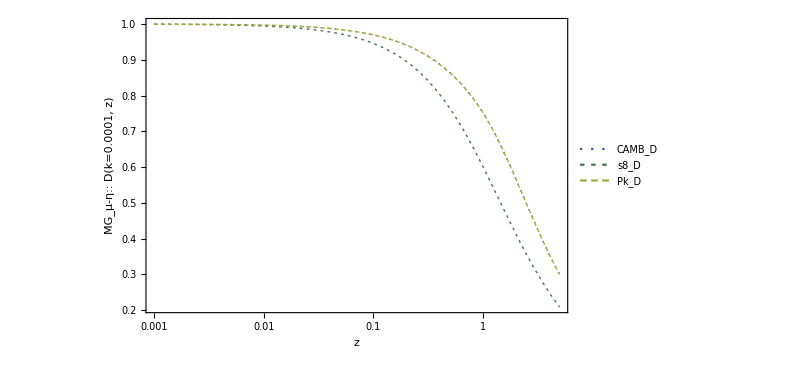

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.0001;  (*Differences only at very large scales*)
LogLinearPlot[{growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz],growthRatioPksLinTabInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"CAMB_D","s8_D","Pk_D"}], Scaled[{0.15,0.2}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"D(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.001

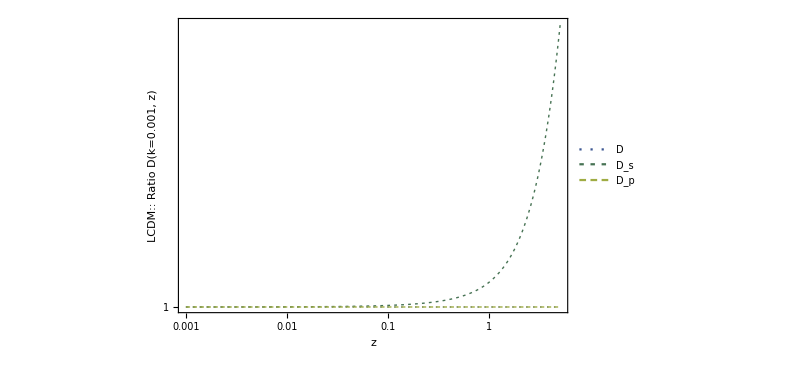

```mathematica
kvall=0.001
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zz, kvall]/growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz]/growthCAMBInterp[modelnum][zz, kvall],growthRatioPksLinTabInterp[modelnum][zz,kvall]/growthCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.25,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,14], Style[modelname<>":: "<>"Ratio D(k="<>ToString[kvall]<>", z)", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

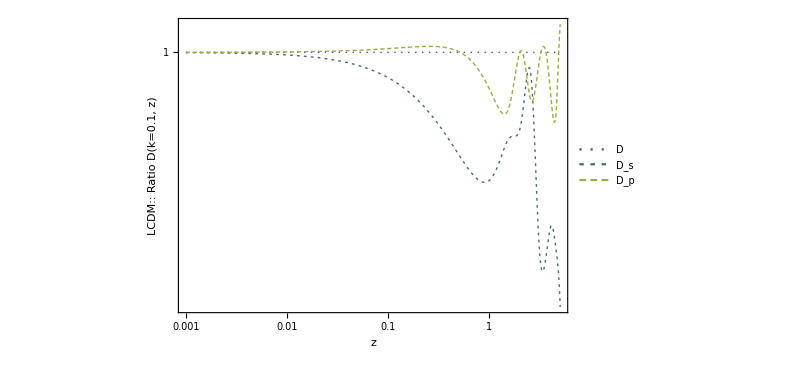

```mathematica
kvall=0.1
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zz, kvall]/growthCAMBInterp[modelnum][zz, kvall],s8growthInterp[modelnum][zz]/growthCAMBInterp[modelnum][zz, kvall],growthRatioPksLinTabInterp[modelnum][zz,kvall]/growthCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.25,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,14], Style[modelname<>":: "<>"Ratio D(k="<>ToString[kvall]<>", z)", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

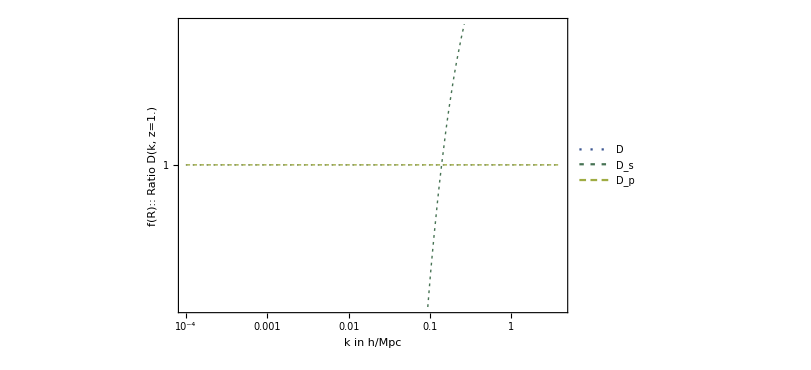

```mathematica
kvall=0.001;
zvall=1.0;
modelnum=3;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{growthCAMBInterp[modelnum][zvall, kk]/growthCAMBInterp[modelnum][zvall, kk],s8growthInterp[modelnum][zvall]/growthCAMBInterp[modelnum][zvall, kk],growthRatioPksLinTabInterp[modelnum][zvall,kk]/growthCAMBInterp[modelnum][zvall, kk]}, {kk,0.0001,4.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"D","D_s","D_p"}], Scaled[{0.8,0.5}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,14], Style[modelname<>":: "<>"Ratio D(k, z="<>ToString[zvall]<>")", Bold, 14]} , ImageSize->600, FrameTicksStyle->Directive[Black,14],
PlotRange->{0.99,1.01}(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

## Plot LCDM different options for Growth Rate f(k,z)

```mathematica
Names["*Interp"]
```

{fgRatioPksLinInterp,fgRatioPksNonLinInterp,fgrowthrateCAMBInterp,growthCAMBInterp,growthRatioPksLinTabInterp,growthRatioPksNonLinTabInterp,pkLinInterp,pkNonLinInterp,s8fgrowthrateInterp,s8growthInterp}

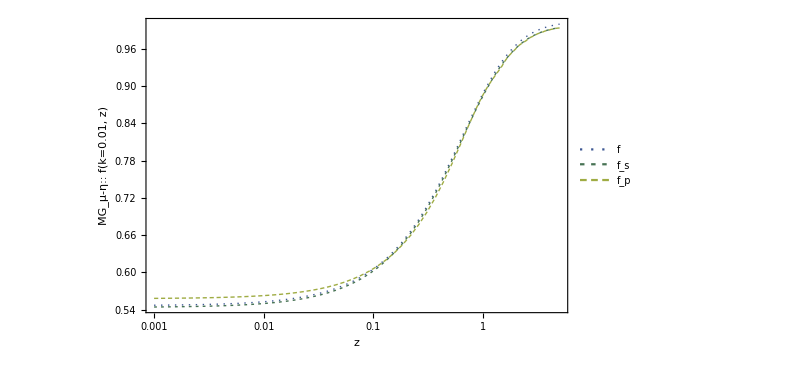

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.01;
LogLinearPlot[{fgrowthrateCAMBInterp[modelnum][zz, kvall],s8fgrowthrateInterp[modelnum][zz],fgRatioPksLinInterp[modelnum][zz,kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.15,0.7}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"f(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

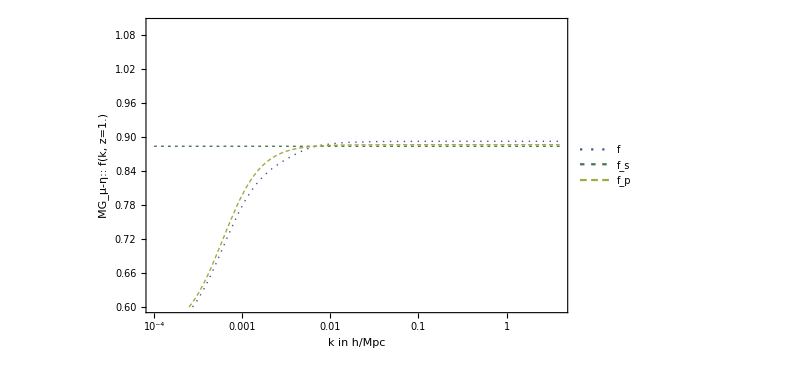

```mathematica
modelnum=4;
modelname=modelnum/.modelsnamerule;
kvall=0.001;
zvall=1.0;
LogLinearPlot[{fgrowthrateCAMBInterp[modelnum][zvall, kkk],s8fgrowthrateInterp[modelnum][zvall],fgRatioPksLinInterp[modelnum][zvall,kkk]}, (*{zz,0.001,5.0}*){kkk,0.0001,4},
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.3}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"f(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->{0.6,1.1}(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

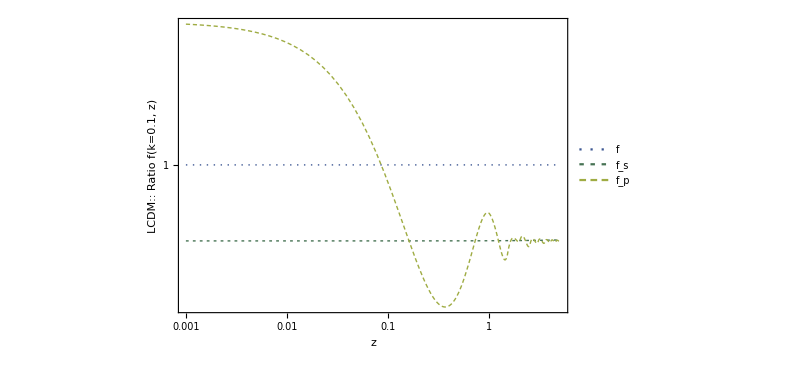

```mathematica
kvall=0.1
modelnum=0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{fgrowthrateCAMBInterp[modelnum][zz, kvall]/fgrowthrateCAMBInterp[modelnum][zz, kvall],s8fgrowthrateInterp[modelnum][zz]/fgrowthrateCAMBInterp[modelnum][zz, kvall],fgRatioPksLinInterp[modelnum][zz,kvall]/fgrowthrateCAMBInterp[modelnum][zz, kvall]}, {zz,0.001,5.0}(*{kkk,0.0001,4}*),
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.75}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["z", Bold,16], Style[modelname<>":: "<>"Ratio f(k="<>ToString[kvall]<>", z)", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```

0.1

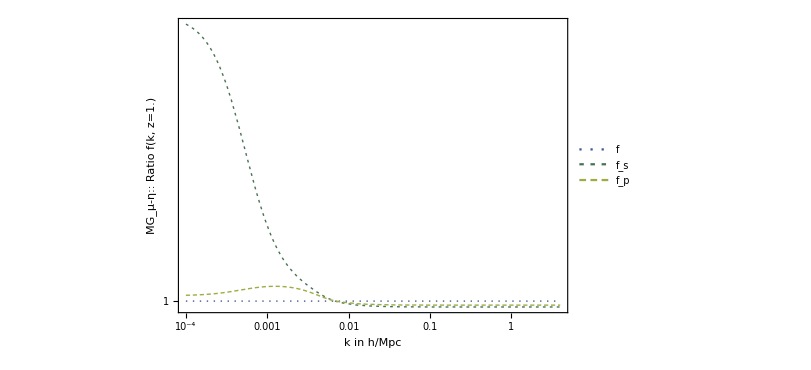

```mathematica
kvall=0.1
modelnum=4;
zvall=1.0;
modelname=modelnum/.modelsnamerule;
LogLogPlot[{fgrowthrateCAMBInterp[modelnum][zvall, kkk]/fgrowthrateCAMBInterp[modelnum][zvall, kkk],s8fgrowthrateInterp[modelnum][zvall]/fgrowthrateCAMBInterp[modelnum][zvall, kkk],fgRatioPksLinInterp[modelnum][zvall,kkk]/fgrowthrateCAMBInterp[modelnum][zvall, kkk]}, (*{zz,0.001,5.0}*){kkk,0.0001,4},
PlotLegends->Placed[LineLegend[{"f","f_s","f_p"}], Scaled[{0.85,0.75}]], PlotStyle->overallStyles, Frame->True, FrameLabel->{Style["k in h/Mpc", Bold,16], Style[modelname<>":: "<>"Ratio f(k, z="<>ToString[zvall]<>")", Bold, 16]} , ImageSize->600, FrameTicksStyle->Directive[Black,16],
PlotRange->All(*Epilog->Inset[raplonl[plotmodlist,zplot,linBool], Scaled[{0.5,0.3}]]*)]
```